## Governing ODE and BCs

α Sin[θ] y[x]-α Cos[θ] y[x] y'[x]+k (y'[x]^2+y[x] y''[x])==1

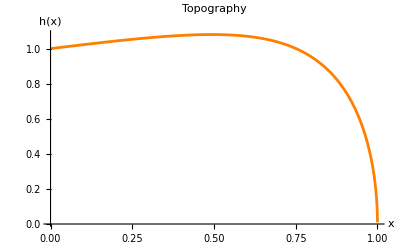

```mathematica
eqn = D[y[x] D[y[x],x],x]*k + α* y[x]*Sin[θ] - α*Cos[θ]*y[x]*y'[x] == 1
BCs = {y[0]==1,y[1]==0.01};
(*Solve numerically*)
Aval = 6;(*ρg/τ - ratio of gravity to yield stress*)
thetaval = π/8;(*slope of the flow*)
kval = 1;(*0<k<1 - corresponds to the viscous term in the z-momentum equation*)
numSol=NDSolve[{eqn/.{α->Aval,θ->thetaval,k->kval},BCs},y[x],{x,0,1}];
Plot[Evaluate[y[x]/. numSol],{x,0,1},AxesLabel->{"x","h(x)"},PlotStyle->Orange,PlotLabel->"Topography",PlotRange->Full]
```